## ODE Using Euler’s Method and Runge-Kutta Order 4

## Jacob Russell

## 1) Write algorithms

```mathematica
euler[a_,b_,alpha_,h_]:=Module[{n=(b-a)/h},
T=Table[a+j*h,{j,0,n}];
Y=Table[alpha,{j,0,n}];
For[k=1,k≤n,k++,
Y⟦k+1⟧=Y⟦k⟧+h*f[T⟦k⟧,Y⟦k⟧]
];
Return[Transpose[{T,Y}]]]
```

```mathematica
rk4[a_,b_,alpha_,h_]:=Module[{n=(b-a)/h,k1,k2,k3,k4},
T=Table[a+j*h,{j,0,n}];
Y=Table[alpha,{j,0,n}];
For[k=1,k≤n,k++,
k1=f[T⟦k⟧,Y⟦k⟧];
k2=f[T⟦k⟧+h/2,Y⟦k⟧+h/2*k1];
k3=f[T⟦k⟧+h/2,Y⟦k⟧+h/2*k2];
k4=f[T⟦k+1⟧+h/2,Y⟦k⟧+h*k3];
Y⟦k+1⟧=Y⟦k⟧+h/6(k1+2*k2+2*k3+k4);
];
Return[Transpose[{T,Y}]]]
```

## 2) Solve ODEs, graph, and compare

## a)

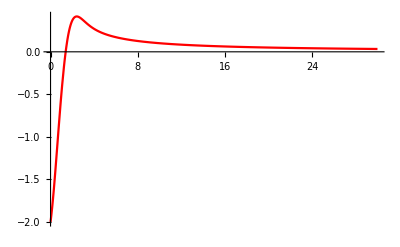

```mathematica
sln1=DSolve[{y'[t]==1-t*y[t],y[0]==-2},y[t],t];
g1=Plot[y[t]/.sln1,{t,0,30},PlotRange->All,PlotStyle->RGBColor[1,0,0]]
```

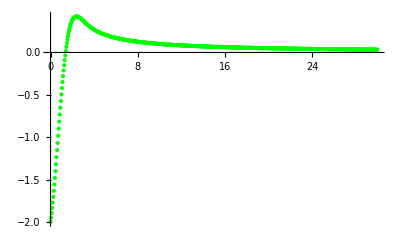

```mathematica
f[t_,y_]=1-t*y;
sl2=euler[0,30,-2,.05];
g2=ListPlot[sl2,PlotRange->All,PlotStyle->RGBColor[0,1,0]]
```

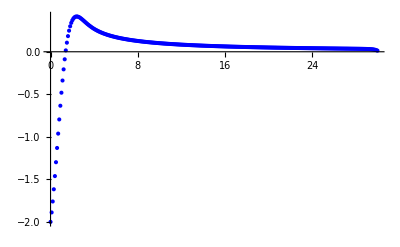

```mathematica
f[t_,y_]=1-t*y;
sl3=rk4[0,30,-2,0.1];
g3=ListPlot[sl3,PlotRange->All,PlotStyle->RGBColor[0,0,1]]
```

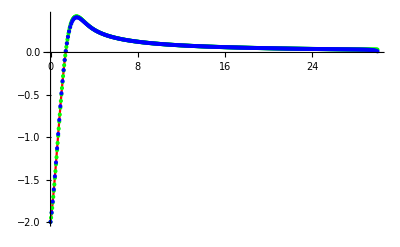

```mathematica
Show[g1,g2,g3]
```

## b)

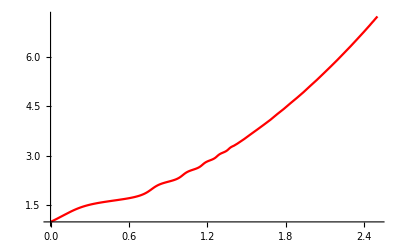

```mathematica
sln1=NDSolve[{y'[t]==1+t y[t]^(1/5)+Sin[y[t]^3],y[0]==1},y[t],{t,0,2.5}];
g1=Plot[y[t]/.sln1,{t,0,2.5},PlotRange->All,PlotStyle->RGBColor[1,0,0]]
```

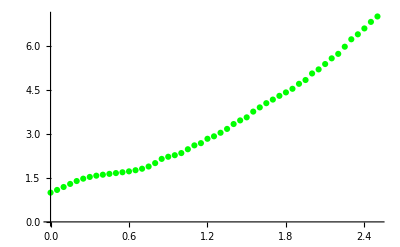

```mathematica
f[t_,y_]=1+t y^(1/5)+Sin[y^3];
sl2=euler[0,2.5,1,0.05];
g2=ListPlot[sl2,PlotRange->All,PlotStyle->RGBColor[0,1,0]]
```

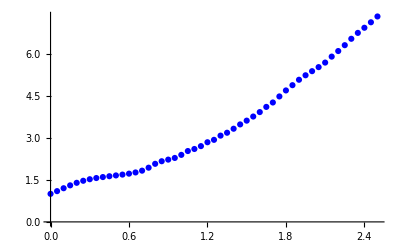

```mathematica
f[t_,y_]=1+t y^(1/5)+Sin[y^3];
sl3=rk4[0,2.5,1,0.05];
g3=ListPlot[sl3,PlotRange->All,PlotStyle->RGBColor[0,0,1]]
```

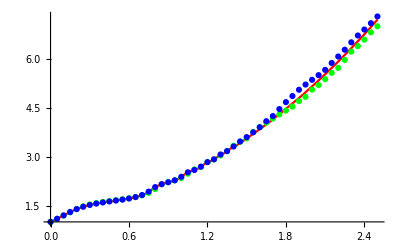

```mathematica
Show[g1,g2,g3]
```

## c)

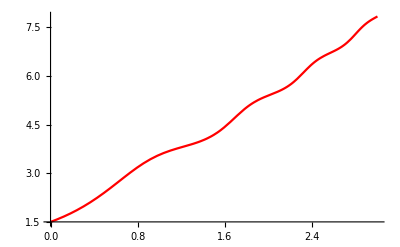

```mathematica
sln1=NDSolve[{y'[t]==y[t]^(1/2)+Sin[t*y[t]],y[0]==1.5},y[t],{t,0,3}];
g1=Plot[y[t]/.sln1,{t,0,3},PlotRange->All,PlotStyle->RGBColor[1,0,0]]
```

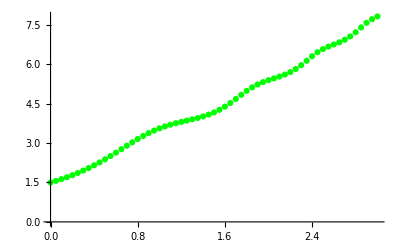

```mathematica
f[t_,y_]=y^(1/2)+Sin[t*y];
sl2=euler[0,3,1.5,.05];
g2=ListPlot[sl2,PlotRange->All,PlotStyle->RGBColor[0,1,0]]
```

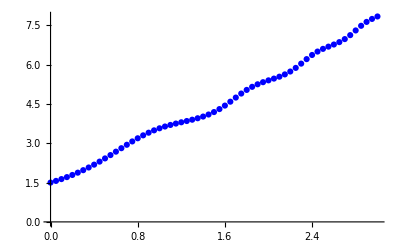

```mathematica
f[t_,y_]=y^(1/2)+Sin[t*y];
sl3=rk4[0,3,1.5,.05];
g3=ListPlot[sl3,PlotRange->All,PlotStyle->RGBColor[0,0,1]]
```

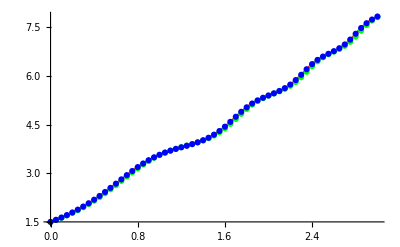

```mathematica
Show[g1,g2,g3]
```

## 3) Application question

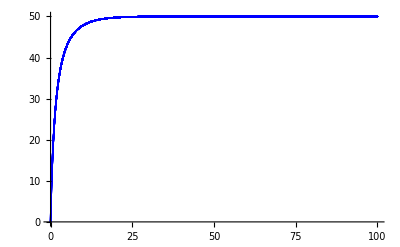

```mathematica
f[t_,y_]=0.01(70-y)(50-y);
sl=rk4[0,100,0,.001];
ListPlot[sl,PlotRange->All,PlotStyle->RGBColor[0,0,1]]
```

Limiting concentration of Y is 50.